#### Functions

```mathematica
ClearAll["Global`*"];

makeLi[i_,parents_List,input_]:=Module[{num,den},If[i===input,
(*input node is left as a free variable*)
L[i],num=kf[i]+Total[Table[kf[i,p] L[p],{p,parents}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,parents}]];
LT[i]*num/den]]

makeAllLi[g_Graph,input_]:=Association[Table[i->makeLi[i,VertexInComponent[g,i,{1}],input],{i,VertexList[g]}]]

expandLi[g_Graph,input_]:=Module[{defs,rules},defs=makeAllLi[g,input];
rules=Thread[L[#]->defs[#]&/@Keys[defs]];
FixedPoint[ReplaceAll[#,rules]&,defs]]


(*RandomDirectedGraphAdjacency[vertexCount_,edgeCount_]:=Module[{elems,adjacencyMatrix,graph},elems=RandomSample@PadRight[ConstantArray[1,edgeCount],vertexCount (vertexCount-1)/2];
adjacencyMatrix=Take[FoldList[RotateLeft,elems,Range[0,vertexCount-2]],All,vertexCount]~LowerTriangularize~-1;
adjacencyMatrix[[2,1]]=1;
adjacencyMatrix=Transpose[adjacencyMatrix];
graph=AdjacencyGraph[adjacencyMatrix]
(*<|"AdjacencyMatrix"->adjacencyMatrix,"Graph"->graph|>*)]*)

RandomDirectedGraphAdjacency[vertexCount_,edgeCount_,p_:0]:=Module[{elems,adjacencyMatrix,graph,backwardConnections,i,j},(*Original forward-only DAG construction*)elems=RandomSample@PadRight[ConstantArray[1,edgeCount],vertexCount (vertexCount-1)/2];
adjacencyMatrix=Take[FoldList[RotateLeft,elems,Range[0,vertexCount-2]],All,vertexCount]~LowerTriangularize~-1;
adjacencyMatrix[[2,1]]=1;
adjacencyMatrix=Transpose[adjacencyMatrix];
(*Add random backward connections with probability p*)If[p>0,
For[i=1,i<=vertexCount,i++,For[j=i+1,j<=vertexCount,j++,
(*Only add backward edge if there's no forward edge and random test passes*)
If[(*adjacencyMatrix[[i,j]]==0&&*)RandomReal[]<p,adjacencyMatrix[[j,i]]=1]]]];
graph=AdjacencyGraph[adjacencyMatrix]]


makeEquationSystem[g_Graph]:=Module[{nodes,eqns},nodes=Sort[VertexList[g]];
eqns=Table[Module[{parents,num,den},parents=VertexInComponent[g,i,{1}];(*incoming neighbors*)
num=kf[i]+Total[Table[kf[i,p] L[p],{p,parents}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,parents}]];
L[i]==LT[i]*num/den],{i,nodes}];
eqns]

makeEquationSystemRHS[g_Graph]:=Module[{nodes,eqns},nodes=Sort[VertexList[g]];
eqns=Table[Module[{parents,num,den},parents=VertexInComponent[g,i,{1}];(*incoming neighbors*)
num=kf[i]+Total[Table[kf[i,p] L[p],{p,parents}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,parents}]];
LT[i]*num/den-L[i]],{i,nodes}];
eqns]

RandomKFKTParams[g_Graph,input_,dist_:{-1,1}]:=Module[{nodes,otherNodes,rules},nodes=VertexList[g];
otherNodes=DeleteCases[nodes,input];
rules=Flatten@Table[Module[{nbrs=VertexInComponent[g,node],kfVal,krVal},
kfVal=Exp[RandomReal[dist]];
krVal=Exp[RandomReal[dist]];
Join[{
kf[node]->kfVal,
kt[node]->kfVal+krVal},
Table[Module[{
kfij=Exp[RandomReal[dist]],
krij=Exp[RandomReal[dist]]},
{kf[node,nbr]->kfij,
kt[node,nbr]->kfij+krij}],{nbr,nbrs}]//Flatten]],{node,otherNodes}];
rules]


RandomLTParams[g_Graph,input_,dist_:{-1,1}]:=Module[{nodes,otherNodes,rules},nodes=VertexList[g];
otherNodes=DeleteCases[nodes,input];
rules=Flatten@Table[LT[node]->Exp[RandomReal[dist]],{node,otherNodes}];
rules]

CreateFeedforwardNNGraph[nodesPerLayer_List]:=Module[
{layers,nodes,edges,graph,maxNodes,yCoords,nodePos, cumCounts,idx},

layers=Length[nodesPerLayer];
maxNodes=Max[nodesPerLayer];

(*Maximum number of nodes in any layer*)(*Create a list of nodes*)
(*nodes=Flatten[Table[Table[Subscript[v,i,j],{j,nodesPerLayer[[i]]}],{i,layers}]];
edges=Flatten[Table[DirectedEdge[Subscript[v,i,j],Subscript[v,i+1,k]],{i,layers-1},{j,nodesPerLayer[[i]]},{k,nodesPerLayer[[i+1]]}]];*)

(*Flattened node list as L[1],L[2],...*)
nodes=Table[i,{i,Total[nodesPerLayer]}];
cumCounts=Prepend[Most@Accumulate[nodesPerLayer],0];
idx[i_,j_]:=cumCounts[[i]]+j;
edges=Flatten[Table[DirectedEdge[idx[i,j],idx[i+1,k]],{i,layers-1},{j,nodesPerLayer[[i]]},{k,nodesPerLayer[[i+1]]}]];

(*Calculate y-coordinates to center nodes in each layer*)
yCoords=0.75*Table[Range[-(nodesPerLayer[[i]]-1)/2,(nodesPerLayer[[i]]-1)/2],{i,layers}];
(*Combine x and y coordinates for node positions*)
nodePos=Flatten[Table[Table[{0.5*i,yCoords[[i,j]]},{j,Length[yCoords[[i]]]}],{i,layers}],1];
(*Create the graph*)graph=Graph[nodes,edges,VertexStyle->Black,EdgeStyle->Directive[Black,Thickness[0.005]],VertexCoordinates->AssociationThread[nodes->nodePos],VertexSize->0.15,ImageSize->160];
graph]

upstream[node_]:=Select[nodes,
(*exclude the node itself*)
#!=node&&GraphDistance[g,#,node]<∞&];
downstream[node_]:=Select[nodes,
(*exclude the node itself*)
#!=node&&GraphDistance[g,node,#]<∞&];

convertToNumDenom[x_]:=NumeratorDenominator[Together[x]]
```

#### Scans

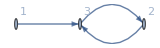

{-L[1]+(kf[1] LT[1])/kt[1],-L[2]+((kf[2]+kf[2,3] L[3]) LT[2])/(kt[2]+kt[2,3] L[3]),-L[3]+((kf[3]+kf[3,1] L[1]+kf[3,2] L[2]) LT[3])/(kt[3]+kt[3,1] L[1]+kt[3,2] L[2])}

```mathematica
(*layerList = {1,2,2,1};
nNodes = Total[layerList];
graph = CreateFeedforwardNNGraph[layerList];*)

graph=Graph[{1->3,2->3,3->2},VertexLabels->"Name"];
nNodes = 3;

(*SeedRandom[30];
nNodes = 3;
nEdges =4;
graph = RandomDirectedGraphAdjacency[nNodes,nEdges, 0.0];*)
(*coords=GraphEmbedding[graph];
graph = RandomDirectedGraphAdjacency[nNodes,nEdges, 0];*)

(*graph=RandomGraph[{nNodes,nEdges},DirectedEdges->True];*)

GraphPlot[graph,VertexLabels->Automatic]

eqs=makeEquationSystemRHS[graph]
```

```mathematica
D[eqs[[3]]+L[3],L[2]]*D[eqs[[2]]+L[2],L[3]]//Simplify
(*D[eqs[[2]]+L[2],L[3]]//Simplify*)
```

((kf[2,3] kt[2]-kf[2] kt[2,3]) (-kt[3,2] (kf[3]+kf[3,1] L[1])+kf[3,2] (kt[3]+kt[3,1] L[1])) LT[2] LT[3])/((kt[3]+kt[3,1] L[1]+kt[3,2] L[2])^2 (kt[2]+kt[2,3] L[3])^2)

```mathematica
layerList = {2,2,2};
nNodes = Total[layerList];
graph = CreateFeedforwardNNGraph[layerList];
eqs=makeEquationSystem[graph]
sol = Solve[eqs[[3;;]],{L[3],L[4],L[5],L[6]}]//Simplify
```

{L[1]==(kf[1] LT[1])/kt[1],L[2]==(kf[2] LT[2])/kt[2],L[3]==((kf[3]+kf[3,1] L[1]+kf[3,2] L[2]) LT[3])/(kt[3]+kt[3,1] L[1]+kt[3,2] L[2]),L[4]==((kf[4]+kf[4,1] L[1]+kf[4,2] L[2]) LT[4])/(kt[4]+kt[4,1] L[1]+kt[4,2] L[2]),L[5]==((kf[5]+kf[5,3] L[3]+kf[5,4] L[4]) LT[5])/(kt[5]+kt[5,3] L[3]+kt[5,4] L[4]),L[6]==((kf[6]+kf[6,3] L[3]+kf[6,4] L[4]) LT[6])/(kt[6]+kt[6,3] L[3]+kt[6,4] L[4])}

{{L[3]→((kf[3]+kf[3,1] L[1]+kf[3,2] L[2]) LT[3])/(kt[3]+kt[3,1] L[1]+kt[3,2] L[2]),L[4]→((kf[4]+kf[4,1] L[1]+kf[4,2] L[2]) LT[4])/(kt[4]+kt[4,1] L[1]+kt[4,2] L[2]),L[5]→((kf[5] (kt[3]+kt[3,1] L[1]+kt[3,2] L[2]) (kt[4]+kt[4,1] L[1]+kt[4,2] L[2])+kf[3,1] kf[5,3] kt[4] L[1] LT[3]+kf[3,1] kf[5,3] kt[4,1] L[1]^2 LT[3]+kf[3,2] kf[5,3] kt[4] L[2] LT[3]+kf[3,2] kf[5,3] kt[4,1] L[1] L[2] LT[3]+kf[3,1] kf[5,3] kt[4,2] L[1] L[2] LT[3]+kf[3,2] kf[5,3] kt[4,2] L[2]^2 LT[3]+kf[3] kf[5,3] (kt[4]+kt[4,1] L[1]+kt[4,2] L[2]) LT[3]+kf[4] kf[5,4] kt[3] LT[4]+kf[4,1] kf[5,4] kt[3] L[1] LT[4]+kf[4] kf[5,4] kt[3,1] L[1] LT[4]+kf[4,1] kf[5,4] kt[3,1] L[1]^2 LT[4]+kf[4,2] kf[5,4] kt[3] L[2] LT[4]+kf[4] kf[5,4] kt[3,2] L[2] LT[4]+kf[4,2] kf[5,4] kt[3,1] L[1] L[2] LT[4]+kf[4,1] kf[5,4] kt[3,2] L[1] L[2] LT[4]+kf[4,2] kf[5,4] kt[3,2] L[2]^2 LT[4]) LT[5])/(kt[5] kt[3,1] kt[4,1] L[1]^2+kt[5] kt[3,2] kt[4,1] L[1] L[2]+kt[5] kt[3,1] kt[4,2] L[1] L[2]+kt[5] kt[3,2] kt[4,2] L[2]^2+kf[3] kt[4,1] kt[5,3] L[1] LT[3]+kf[3,1] kt[4,1] kt[5,3] L[1]^2 LT[3]+kf[3] kt[4,2] kt[5,3] L[2] LT[3]+kf[3,2] kt[4,1] kt[5,3] L[1] L[2] LT[3]+kf[3,1] kt[4,2] kt[5,3] L[1] L[2] LT[3]+kf[3,2] kt[4,2] kt[5,3] L[2]^2 LT[3]+kt[4] (kt[5] (kt[3,1] L[1]+kt[3,2] L[2])+kt[5,3] (kf[3]+kf[3,1] L[1]+kf[3,2] L[2]) LT[3])+kf[4] kt[3,1] kt[5,4] L[1] LT[4]+kf[4,1] kt[3,1] kt[5,4] L[1]^2 LT[4]+kf[4] kt[3,2] kt[5,4] L[2] LT[4]+kf[4,2] kt[3,1] kt[5,4] L[1] L[2] LT[4]+kf[4,1] kt[3,2] kt[5,4] L[1] L[2] LT[4]+kf[4,2] kt[3,2] kt[5,4] L[2]^2 LT[4]+kt[3] (kt[4] kt[5]+kt[5] (kt[4,1] L[1]+kt[4,2] L[2])+kt[5,4] (kf[4]+kf[4,1] L[1]+kf[4,2] L[2]) LT[4])),L[6]→((kf[6] (kt[3]+kt[3,1] L[1]+kt[3,2] L[2]) (kt[4]+kt[4,1] L[1]+kt[4,2] L[2])+kf[3,1] kf[6,3] kt[4] L[1] LT[3]+kf[3,1] kf[6,3] kt[4,1] L[1]^2 LT[3]+kf[3,2] kf[6,3] kt[4] L[2] LT[3]+kf[3,2] kf[6,3] kt[4,1] L[1] L[2] LT[3]+kf[3,1] kf[6,3] kt[4,2] L[1] L[2] LT[3]+kf[3,2] kf[6,3] kt[4,2] L[2]^2 LT[3]+kf[3] kf[6,3] (kt[4]+kt[4,1] L[1]+kt[4,2] L[2]) LT[3]+kf[4] kf[6,4] kt[3] LT[4]+kf[4,1] kf[6,4] kt[3] L[1] LT[4]+kf[4] kf[6,4] kt[3,1] L[1] LT[4]+kf[4,1] kf[6,4] kt[3,1] L[1]^2 LT[4]+kf[4,2] kf[6,4] kt[3] L[2] LT[4]+kf[4] kf[6,4] kt[3,2] L[2] LT[4]+kf[4,2] kf[6,4] kt[3,1] L[1] L[2] LT[4]+kf[4,1] kf[6,4] kt[3,2] L[1] L[2] LT[4]+kf[4,2] kf[6,4] kt[3,2] L[2]^2 LT[4]) LT[6])/(kt[6] kt[3,1] kt[4,1] L[1]^2+kt[6] kt[3,2] kt[4,1] L[1] L[2]+kt[6] kt[3,1] kt[4,2] L[1] L[2]+kt[6] kt[3,2] kt[4,2] L[2]^2+kf[3] kt[4,1] kt[6,3] L[1] LT[3]+kf[3,1] kt[4,1] kt[6,3] L[1]^2 LT[3]+kf[3] kt[4,2] kt[6,3] L[2] LT[3]+kf[3,2] kt[4,1] kt[6,3] L[1] L[2] LT[3]+kf[3,1] kt[4,2] kt[6,3] L[1] L[2] LT[3]+kf[3,2] kt[4,2] kt[6,3] L[2]^2 LT[3]+kt[4] (kt[6] (kt[3,1] L[1]+kt[3,2] L[2])+kt[6,3] (kf[3]+kf[3,1] L[1]+kf[3,2] L[2]) LT[3])+kf[4] kt[3,1] kt[6,4] L[1] LT[4]+kf[4,1] kt[3,1] kt[6,4] L[1]^2 LT[4]+kf[4] kt[3,2] kt[6,4] L[2] LT[4]+kf[4,2] kt[3,1] kt[6,4] L[1] L[2] LT[4]+kf[4,1] kt[3,2] kt[6,4] L[1] L[2] LT[4]+kf[4,2] kt[3,2] kt[6,4] L[2]^2 LT[4]+kt[3] (kt[4] kt[6]+kt[6] (kt[4,1] L[1]+kt[4,2] L[2])+kt[6,4] (kf[4]+kf[4,1] L[1]+kf[4,2] L[2]) LT[4]))}}

```mathematica
kfktRules=RandomKFKTParams[graph,1,{-1,4}];
ltRules=RandomLTParams[graph,1,{-1,4}];
allRules=Join[kfktRules,ltRules];

L5= L[5]/.sol[[1]][[3]]/.allRules;
L6= L[6]/.sol[[1]][[4]]/.allRules;
Collect[Numerator[L5],{L[1],L[2]}]
(*CoefficientArrays[Numerator[L5],{L[1],L[2]}]*)
```

5.52718×10^7+2.53201×10^6 L[1]^2+5.88447×10^6 L[2]+144807. L[2]^2+L[1] (3.78682×10^7+2.06242×10^6 L[2])

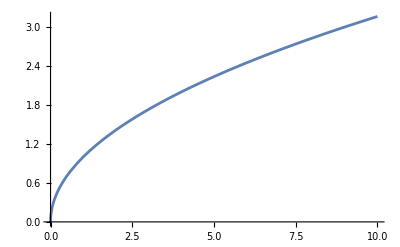

```mathematica
Plot[Sqrt[x],{x,0,10}]
```

```mathematica
graph=Graph[{1->2,2->1},VertexLabels->"Name"];
nNodes = 2;
eqs=makeEquationSystem[graph]
eqsrhs=makeEquationSystemRHS[graph]
deriv=D[eqsrhs[[1]]+L[1],L[2]]*D[eqsrhs[[2]]+L[2],L[1]]//Simplify
sol=Solve[eqs,{L[1],L[2]}]//Simplify
```

{L[1]==((kf[1]+kf[1,2] L[2]) LT[1])/(kt[1]+kt[1,2] L[2]),L[2]==((kf[2]+kf[2,1] L[1]) LT[2])/(kt[2]+kt[2,1] L[1])}

{-L[1]+((kf[1]+kf[1,2] L[2]) LT[1])/(kt[1]+kt[1,2] L[2]),-L[2]+((kf[2]+kf[2,1] L[1]) LT[2])/(kt[2]+kt[2,1] L[1])}

((kf[1,2] kt[1]-kf[1] kt[1,2]) (kf[2,1] kt[2]-kf[2] kt[2,1]) LT[1] LT[2])/((kt[2]+kt[2,1] L[1])^2 (kt[1]+kt[1,2] L[2])^2)

{{L[1]→1/(2 (kt[1] kt[2,1]+kf[2,1] kt[1,2] LT[2]))(-kt[1] kt[2]+kf[1] kt[2,1] LT[1]-kf[2] kt[1,2] LT[2]+kf[1,2] kf[2,1] LT[1] LT[2]+√(4 LT[1] (kf[1] kt[2]+kf[2] kf[1,2] LT[2]) (kt[1] kt[2,1]+kf[2,1] kt[1,2] LT[2])+(kt[1] kt[2]-kf[1] kt[2,1] LT[1]+(kf[2] kt[1,2]-kf[1,2] kf[2,1] LT[1]) LT[2])^2)),L[2]→1/(2 (kt[2] kt[1,2]+kf[1,2] kt[2,1] LT[1]))(-kt[1] kt[2]-kf[1] kt[2,1] LT[1]+kf[2] kt[1,2] LT[2]+kf[1,2] kf[2,1] LT[1] LT[2]+√(4 LT[1] (kf[1] kt[2]+kf[2] kf[1,2] LT[2]) (kt[1] kt[2,1]+kf[2,1] kt[1,2] LT[2])+(kt[1] kt[2]-kf[1] kt[2,1] LT[1]+(kf[2] kt[1,2]-kf[1,2] kf[2,1] LT[1]) LT[2])^2))},{L[1]→-1/(2 (kt[1] kt[2,1]+kf[2,1] kt[1,2] LT[2]))(kt[1] kt[2]-kf[1] kt[2,1] LT[1]+kf[2] kt[1,2] LT[2]-kf[1,2] kf[2,1] LT[1] LT[2]+√(4 LT[1] (kf[1] kt[2]+kf[2] kf[1,2] LT[2]) (kt[1] kt[2,1]+kf[2,1] kt[1,2] LT[2])+(kt[1] kt[2]-kf[1] kt[2,1] LT[1]+(kf[2] kt[1,2]-kf[1,2] kf[2,1] LT[1]) LT[2])^2)),L[2]→-1/(2 (kt[2] kt[1,2]+kf[1,2] kt[2,1] LT[1]))(kt[1] kt[2]+kf[1] kt[2,1] LT[1]-kf[2] kt[1,2] LT[2]-kf[1,2] kf[2,1] LT[1] LT[2]+√(4 LT[1] (kf[1] kt[2]+kf[2] kf[1,2] LT[2]) (kt[1] kt[2,1]+kf[2,1] kt[1,2] LT[2])+(kt[1] kt[2]-kf[1] kt[2,1] LT[1]+(kf[2] kt[1,2]-kf[1,2] kf[2,1] LT[1]) LT[2])^2))}}

```mathematica
deriv/.sol[[1]]//Simplify
```

((kf[1,2] kt[1]-kf[1] kt[1,2]) (kf[2,1] kt[2]-kf[2] kt[2,1]) LT[1] LT[2])/((kt[2]+1/(2 (kt[1] kt[2,1]+kf[2,1] kt[1,2] LT[2]))kt[2,1] (-kt[1] kt[2]+kf[1] kt[2,1] LT[1]-kf[2] kt[1,2] LT[2]+kf[1,2] kf[2,1] LT[1] LT[2]+√(4 LT[1] (kf[1] kt[2]+kf[2] kf[1,2] LT[2]) (kt[1] kt[2,1]+kf[2,1] kt[1,2] LT[2])+(kt[1] kt[2]-kf[1] kt[2,1] LT[1]+(kf[2] kt[1,2]-kf[1,2] kf[2,1] LT[1]) LT[2])^2)))^2 (kt[1]+1/(2 (kt[2] kt[1,2]+kf[1,2] kt[2,1] LT[1]))kt[1,2] (-kt[1] kt[2]-kf[1] kt[2,1] LT[1]+kf[2] kt[1,2] LT[2]+kf[1,2] kf[2,1] LT[1] LT[2]+√(4 LT[1] (kf[1] kt[2]+kf[2] kf[1,2] LT[2]) (kt[1] kt[2,1]+kf[2,1] kt[1,2] LT[2])+(kt[1] kt[2]-kf[1] kt[2,1] LT[1]+(kf[2] kt[1,2]-kf[1,2] kf[2,1] LT[1]) LT[2])^2)))^2)

```mathematica
kfktRules=RandomKFKTParams[graph,1,{-1,4}];
ltRules=RandomLTParams[graph,1,{-1,4}];
allRules=Join[kfktRules,ltRules];

rhs = makeEquationSystemRHS[graph][[;;]]/.allRules
```

{-L[1]+(kf[1] LT[1])/kt[1],-L[2]+(1.42411 (1.72665+1.73399 L[3]))/(49.2307+7.86336 L[3]),(45.0274 (0.489728+21.4724 L[1]+0.958317 L[2]))/(24.943+21.9667 L[1]+1.4358 L[2])-L[3]}

```mathematica
ContourPlot[]
```

```mathematica
rhs = makeEquationSystemRHS[graph][[;;]]
```

{-L[1]+(kf[1] LT[1])/kt[1],-L[2]+((kf[2]+kf[2,3] L[3]) LT[2])/(kt[2]+kt[2,3] L[3]),-L[3]+((kf[3]+kf[3,1] L[1]+kf[3,2] L[2]) LT[3])/(kt[3]+kt[3,1] L[1]+kt[3,2] L[2])}

```mathematica
num=kf[i]+Total[Table[kf[i,p] L[p],{p,{1,2}}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,{1,2}}]];
D[LT[i]*num/den,L[1]]//Simplify
```

((-kt[i,1] (kf[i]+kf[i,2] L[2])+kf[i,1] (kt[i]+kt[i,2] L[2])) LT[i])/(kt[i]+kt[i,1] L[1]+kt[i,2] L[2])^2

```mathematica
eqs=makeEquationSystem[graph]
sol=Solve[eqs[[2;;nNodes]],Table[L[i],{i,2,nNodes}]]//Simplify;
(*L2expr=L[2]/.sol[[1]];
L3expr=L[3]/.sol[[1]];*)
expr = L[nNodes]/.sol[[2]];
allSimplePaths=FindPath[graph,1,nNodes,Infinity,All];
numberOfSimplePaths=Length[allSimplePaths]
(*num=D[L3expr,L[1]]//Simplify//Together//Numerator
Collect[num,L[1]]//TraditionalForm
CoefficientList[num,L[1]]//TraditionalForm*)
```

{L[1]==(kf[1] LT[1])/kt[1],L[3]==((kf[3]+kf[3,1] L[1]+kf[3,2] L[2]) LT[3])/(kt[3]+kt[3,1] L[1]+kt[3,2] L[2]),L[2]==((kf[2]+kf[2,3] L[3]) LT[2])/(kt[2]+kt[2,3] L[3])}

1

```mathematica
L2expr=L[2]/.sol[[2]]/.L[1]->0//Simplify
L3expr=L[3]/.sol[[2]]/.L[1]->0//Simplify
```

1/(2 (kt[2] kt[3,2]+kf[3,2] kt[2,3] LT[3]))(-kt[2] kt[3]+kf[2] kt[3,2] LT[2]-kf[3] kt[2,3] LT[3]+kf[2,3] kf[3,2] LT[2] LT[3]+√(4 (kf[3] kt[2]+kf[2] kf[3,2] LT[2]) (kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]) LT[3]+(kt[2] kt[3]+kf[2] kt[3,2] LT[2]-(kf[3] kt[2,3]+kf[2,3] kf[3,2] LT[2]) LT[3])^2))

1/(2 (kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]))(-kt[2] kt[3]-kf[2] kt[3,2] LT[2]+kf[3] kt[2,3] LT[3]+kf[2,3] kf[3,2] LT[2] LT[3]+√(4 (kf[3] kt[2]+kf[2] kf[3,2] LT[2]) (kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]) LT[3]+(kt[2] kt[3]+kf[2] kt[3,2] LT[2]-(kf[3] kt[2,3]+kf[2,3] kf[3,2] LT[2]) LT[3])^2))

```mathematica
L3expr/L2expr//Simplify
```

((kt[2] kt[3,2]+kf[3,2] kt[2,3] LT[3]) (-kt[2] kt[3]-kf[2] kt[3,2] LT[2]+kf[3] kt[2,3] LT[3]+kf[2,3] kf[3,2] LT[2] LT[3]+√(4 (kf[3] kt[2]+kf[2] kf[3,2] LT[2]) (kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]) LT[3]+(kt[2] kt[3]+kf[2] kt[3,2] LT[2]-(kf[3] kt[2,3]+kf[2,3] kf[3,2] LT[2]) LT[3])^2)))/((kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]) (-kt[2] kt[3]+kf[2] kt[3,2] LT[2]-kf[3] kt[2,3] LT[3]+kf[2,3] kf[3,2] LT[2] LT[3]+√(4 (kf[3] kt[2]+kf[2] kf[3,2] LT[2]) (kt[3] kt[2,3]+kf[2,3] kt[3,2] LT[2]) LT[3]+(kt[2] kt[3]+kf[2] kt[3,2] LT[2]-(kf[3] kt[2,3]+kf[2,3] kf[3,2] LT[2]) LT[3])^2)))

```mathematica
D[expr,L[1]]//Simplify//TraditionalForm
```

1/(2 (LT(2) kf(2,3) kt(3,2)+L(1) kt(3,1) kt(2,3)+kt(3) kt(2,3))^2)(kt(2,3) kt(3,1) (-L(1) LT(3) kf(3,1) kt(2,3)+√((-LT(3) (L(1) kf(3,1) kt(2,3)+kf(3) kt(2,3)+LT(2) kf(2,3) kf(3,2))+kf(2) LT(2) kt(3,2)+kt(2) (L(1) kt(3,1)+kt(3)))^2+4 LT(3) (kt(2) L(1) kf(3,1)+kf(2) LT(2) kf(3,2)+kf(3) kt(2)) (LT(2) kf(2,3) kt(3,2)+L(1) kt(3,1) kt(2,3)+kt(3) kt(2,3)))+kf(2) LT(2) kt(3,2)-kf(3) LT(3) kt(2,3)-LT(2) LT(3) kf(2,3) kf(3,2)+kt(2) L(1) kt(3,1)+kt(2) kt(3))-(LT(2) kf(2,3) kt(3,2)+L(1) kt(3,1) kt(2,3)+kt(3) kt(2,3)) ((4 LT(3) kt(2,3) kt(3,1) (kt(2) L(1) kf(3,1)+kf(2) LT(2) kf(3,2)+kf(3) kt(2))+4 kt(2) LT(3) kf(3,1) (LT(2) kf(2,3) kt(3,2)+L(1) kt(3,1) kt(2,3)+kt(3) kt(2,3))+2 (kt(2) kt(3,1)-LT(3) kf(3,1) kt(2,3)) (-LT(3) (L(1) kf(3,1) kt(2,3)+kf(3) kt(2,3)+LT(2) kf(2,3) kf(3,2))+kf(2) LT(2) kt(3,2)+kt(2) (L(1) kt(3,1)+kt(3))))/(2 √((-LT(3) (L(1) kf(3,1) kt(2,3)+kf(3) kt(2,3)+LT(2) kf(2,3) kf(3,2))+kf(2) LT(2) kt(3,2)+kt(2) (L(1) kt(3,1)+kt(3)))^2+4 LT(3) (kt(2) L(1) kf(3,1)+kf(2) LT(2) kf(3,2)+kf(3) kt(2)) (LT(2) kf(2,3) kt(3,2)+L(1) kt(3,1) kt(2,3)+kt(3) kt(2,3))))-LT(3) kf(3,1) kt(2,3)+kt(2) kt(3,1)))

```mathematica
expr = expandLi[ graph,1][nNodes];
num = convertToNumDenom[expr][[1]];
num = convertToNumDenom[expr][[1]];
denom = convertToNumDenom[expr][[2]];
CoefficientList[num,L[1]]//Length
CoefficientList[denom,L[1]]//Length

allSimplePaths=FindPath[graph,1,nNodes,Infinity,All];
numberOfSimplePaths=Length[allSimplePaths]
```

2

2

1

-Graphics-

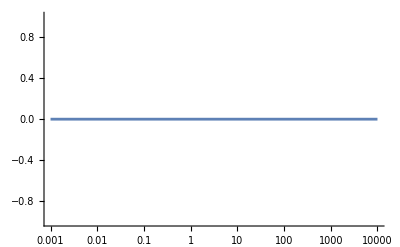

```mathematica
kfktRules=RandomKFKTParams[graph,1,{-1,4}];
ltRules=RandomLTParams[graph,1,{-1,4}];
allRules=Join[kfktRules,ltRules];

rhs = makeEquationSystemRHS[graph][[2;;]]/.allRules;

lower = 10^-3;
upper = 10^4;
L1Array = PowerRange[lower,upper,1.1];

(*LVars = Table[L[i],{i,1,nNodes}];
sols = Table[LVars[[2;;]]/.FindRoot[rhs/.L[1]->L1Array[[m]],Table[{LVars[[i]],LT[i]/.ltRules},{i,2,nNodes}],AccuracyGoal->10,PrecisionGoal->10],{m,1,Length[L1Array]}];
solFunc:=Interpolation[Transpose[{L1Array,sols[[;;,nNodes-1]]}]]*)

solFuncc[r_]:=Evaluate[expr/.allRules/.L[1]->r];
gradFunc = solFuncc';
LogLinearPlot[solFuncc[r],{r,lower,upper},PlotRange->Full]
LogLinearPlot[gradFunc[r],{r,lower,upper},PlotRange->Full]
```

```mathematica
(*layerList = {1,2,1};
nNodes = Total[layerList];
graph = CreateFeedforwardNNGraph[layerList]*)
SeedRandom[34];
expr = L[nNodes]/.sol[[2]];
lower = 10^-3;
upper = 10^3;
nPoints = 200;

L1Array = PowerRange[lower,upper,1.1];
samplePts=Table[10^r,{r,Log10[1.01lower],Log10[0.99upper],(Log10[upper]-Log10[lower])/nPoints}]//N;

signChangesList = {};

Do[

kfktRules=RandomKFKTParams[graph,1,{-4,4}];
     ltRules=RandomLTParams[graph,1,{-4,4}];
allRules=Join[kfktRules,ltRules];

(*rhs = makeEquationSystemRHS[graph][[2;;]]/.allRules;
LVars = Table[L[i],{i,1,nNodes}];
sols = Table[LVars[[2;;]]/.FindRoot[rhs/.L[1]->L1Array[[m]],Table[{LVars[[i]],LT[i]/.ltRules},{i,2,nNodes}],AccuracyGoal->10,PrecisionGoal->10,MaxIterations->5000,Method->{"Newton", "StepControl" -> "TrustRegion"}],{m,1,Length[L1Array]}];

solFunc:=Interpolation[Transpose[{L1Array,sols[[;;,nNodes-1]]}]];
gradFunc = solFunc';*)

     solFuncc[r_]:=Evaluate[expr/.allRules/.L[1]->r];
gradFunc=solFuncc';

  signChanges=Partition[samplePts,2,1]/. {a_,b_}:>If[Sign[gradFunc[a]]!=Sign[gradFunc[b]],{a,b},Nothing];

AppendTo[signChangesList,Length[signChanges]];
,{nIter,1,10000}
]//AbsoluteTiming
```

{43.2864,Null}

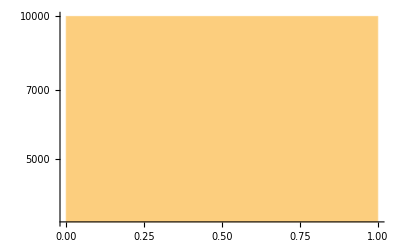

0

```mathematica
Histogram[signChangesList,ScalingFunctions->{None,"Log"}]
Max[signChangesList]
```

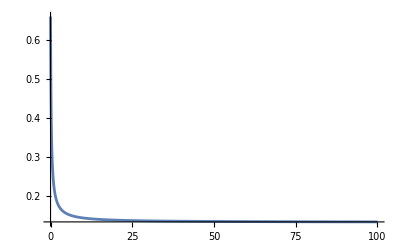

```mathematica
Plot[solFuncc[r],{r,0,100},PlotRange->Full]
```

```mathematica
Together[expr]
```

$Aborted

```mathematica
num
```

```mathematica
mat = {{0,0,0,0,0},{kdxr x, kdx, 0, 0,  0}, {0, kdyx y, kdy, 0, 0},{kdzr r, 0, 0, kdz, 0},{0, kdsx s, kdsy s, kdsz s, kds}}
mat  = mat[[2;;,2;;]]
Rvec = {kdxr x, 0, kdzr z, 0};
Adjugate[mat].Rvec
```

{{0,0,0,0,0},{kdxr x,kdx,0,0,0},{0,kdyx y,kdy,0,0},{kdzr r,0,0,kdz,0},{0,kdsx s,kdsy s,kdsz s,kds}}

{{kdx,0,0,0},{kdyx y,kdy,0,0},{0,0,kdz,0},{kdsx s,kdsy s,kdsz s,kds}}

{kds kdxr kdy kdz x,-kds kdxr kdyx kdz x y,kds kdx kdy kdzr z,kdxr x (-kdsx kdy kdz s+kdsy kdyx kdz s y)-kdsz kdx kdy kdzr s z}

#### RXYZS example

```mathematica
(*eqX=-ktX X+kfX lX0-ktXR X lR0+kfXR lX0 lR0-ktXS X S+kfXS lX0 S;
eqY=-ktY Y+kfY lY0-ktYX Y X+kfYX lY0 X;
eqZ=-ktZ Z+kfZ lZ0-ktZR Z lR0+kfZR lZ0 lR0-ktZS Z S+kfZS lZ0 S;
eqS=-ktS S+kfS lS0-ktSX S X+kfSX lS0 X-ktSY S Y+kfSY lS0 Y-ktSZ S Z+kfSZ lS0 Z;*)

eqX=-ktX X+kfX lX0-ktXR X lR0+kfXR lX0 lR0;
eqY=-ktY Y+kfY lY0-ktYX Y X+kfYX lY0 X;
eqZ=-ktZ Z+kfZ lZ0-ktZR Z lR0+kfZR lZ0 lR0;
eqS=-ktS S+kfS lS0-ktSX S X+kfSX lS0 X-ktSY S Y+kfSY lS0 Y-ktSZ S Z+kfSZ lS0 Z;

Rdot={eqX,eqY,eqZ,eqS};

(*---Compute Jacobian wrt state variables (DReDCbar)---*)
vars={X,Y,Z,S};
DReDCbar=D[Rdot,{vars}];

(*---Compute Jacobian wrt ligand parameters (DReDl0)---*)
l0vars={lR0,lX0,lY0,lZ0,lS0};
DReDl0=D[Rdot,{l0vars}];


matProd=Adjugate[DReDCbar].DReDl0[[;;,1]]//Expand;
expr=matProd[[4]];
Collect[expr,{S}]//Simplify

eqs={eqX,eqY,eqZ,eqS};
```

-kfSZ kfZR ktX ktY lS0 lZ0-kfSZ kfZR ktXR ktY lR0 lS0 lZ0+kfXR ktSX ktY ktZ lX0 S+kfXR ktSX ktY ktZR lR0 lX0 S+kfXR kfYX ktSY ktZ lX0 lY0 S+kfXR kfYX ktSY ktZR lR0 lX0 lY0 S+kfZR ktSZ ktX ktY lZ0 S+kfZR ktSZ ktXR ktY lR0 lZ0 S-kfSZ kfZR ktX ktYX lS0 lZ0 X-kfSZ kfZR ktXR ktYX lR0 lS0 lZ0 X-ktSX ktXR ktY ktZ S X-ktSX ktXR ktY ktZR lR0 S X+kfXR ktSX ktYX ktZ lX0 S X+kfXR ktSX ktYX ktZR lR0 lX0 S X-kfYX ktSY ktXR ktZ lY0 S X-kfYX ktSY ktXR ktZR lR0 lY0 S X+kfZR ktSZ ktX ktYX lZ0 S X+kfZR ktSZ ktXR ktYX lR0 lZ0 S X-ktSX ktXR ktYX ktZ S X^2-ktSX ktXR ktYX ktZR lR0 S X^2-kfSX (ktZ+ktZR lR0) lS0 (kfXR lX0-ktXR X) (ktY+ktYX X)-kfXR ktSY ktYX ktZ lX0 S Y-kfXR ktSY ktYX ktZR lR0 lX0 S Y+ktSY ktXR ktYX ktZ S X Y+ktSY ktXR ktYX ktZR lR0 S X Y-kfSY (ktZ+ktZR lR0) lS0 (kfXR lX0-ktXR X) (kfYX lY0-ktYX Y)+kfSZ ktX ktY ktZR lS0 Z+kfSZ ktXR ktY ktZR lR0 lS0 Z-ktSZ ktX ktY ktZR S Z-ktSZ ktXR ktY ktZR lR0 S Z+kfSZ ktX ktYX ktZR lS0 X Z+kfSZ ktXR ktYX ktZR lR0 lS0 X Z-ktSZ ktX ktYX ktZR S X Z-ktSZ ktXR ktYX ktZR lR0 S X Z

```mathematica
(*Define parameter symbols*)
kParams={ktX,kfX,ktXR,kfXR,ktXS,kfXS,ktY,kfY,ktYX,kfYX,ktZ,kfZ,ktZR,kfZR,ktZS,kfZS,ktS,kfS,ktSX,kfSX,ktSY,kfSY,ktSZ,kfSZ};

l0Params={lR0,lX0,lY0,lZ0,lS0};

(*Assign random values satisfying k^t>k^f*)
Table[Module[{
kf=RandomReal[{0.1,50}],kt},
kt=kf+RandomReal[{0.1,50}];(*ensure kt>kf*)
{Symbol[StringReplace[ToString[param],"f"->"t"]]->kt,param->kf}],{param,Select[kParams,StringContainsQ[ToString[#],"f"]&]}]//Flatten//Evaluate;

kAssignments=%;

(*Assign random positive l0s,leaving lR0 unassigned*)
l0Assignments=Thread[{lX0,lY0,lZ0,lS0}->RandomReal[{0.1,2},4]];

(*Combine all assignments (except lR0)*)
paramAssignments=Join[kAssignments,l0Assignments];
```

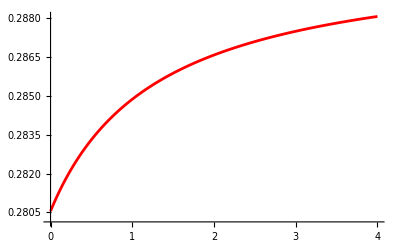

```mathematica
initialGuesses={X,Y,Z,S}/. Thread[{X,Y,Z,S}->RandomReal[{0.1,1.5},4]];
(*Use FindRoot to get one steady state*)
lR0eval = 1;
lR0Range = Range[0,4,.01];
nullVals = {};
solVals = {};
solLength = {};
Do[

sol=Quiet@FindRoot[eqs/. paramAssignments/.lR0->lR0eval,{X,initialGuesses[[1]]},{Y,initialGuesses[[2]]},{Z,initialGuesses[[3]]},{S,initialGuesses[[4]]},MaxIterations->200];
AppendTo[solVals,{lR0eval,S/.sol}];

exprEval=expr/. paramAssignments/.lR0->lR0eval/.sol[[1;;3]];
solDeriv=Quiet@FindRoot[exprEval,{S,initialGuesses[[1]]},
AccuracyGoal->10,
PrecisionGoal->10,
MaxIterations->200000];
AppendTo[nullVals,{lR0eval,S/.solDeriv}];


(*exprEval=expr/. paramAssignments/.sol;
solDeriv=NSolve[exprEval==0,{lR0}];
AppendTo[solLength, Length[solDeriv]];
AppendTo[nullVals,{(lR0/.solDeriv)[[1]],S/.sol}];*)

,{lR0eval,lR0Range}];

Show[
ListPlot[solVals,Joined->True,PlotRange->Automatic,PlotStyle->Red,PlotRange->Full],
ListPlot[nullVals,Joined->True,PlotStyle->Blue](*,
PlotRange->All*)

]
```

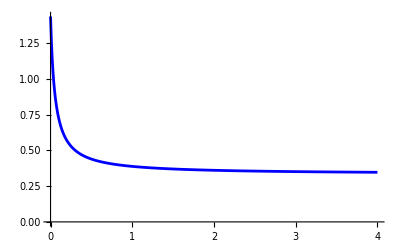

```mathematica
ListPlot[nullVals,Joined->True,PlotStyle->Blue,PlotRange->Full]
```

```mathematica
nullVals
```

{{0.536087,0.286389},{0.505443,0.286416},{0.477106,0.28644},{0.450826,0.286461},{0.426386,0.28648},{0.403599,0.286497},{0.382304,0.286512},{0.362358,0.286526},{0.343638,0.286537},{0.326033,0.286548},{0.309447,0.286556},{0.293793,0.286564},{0.278996,0.286571},{0.264987,0.286576},{0.251705,0.28658},{0.239094,0.286584},{0.227105,0.286587},{0.215692,0.286588},{0.204817,0.28659},{0.19444,0.28659},{0.184529,0.28659},{0.175054,0.286589},{0.165985,0.286588},{0.157298,0.286586},{0.148968,0.286584},{0.140975,0.286581},{0.133298,0.286578},{0.125918,0.286574},{0.11882,0.28657},{0.111986,0.286566},{0.105403,0.286561},{0.0990572,0.286556},{0.0929356,0.286551},{0.0870267,0.286545},{0.0813196,0.286539},{0.0758042,0.286533},{0.0704709,0.286527},{0.0653109,0.28652},{0.0603158,0.286513},{0.0554779,0.286506},{0.05079,0.286499},{0.046245,0.286492},{0.0418366,0.286484},{0.0375587,0.286477},{0.0334056,0.286469},{0.0293719,0.286461},{0.0254525,0.286453},{0.0216427,0.286445},{0.0179379,0.286436},{0.0143338,0.286428},{0.0108265,0.286419},{0.0074119,0.286411},{0.00408655,0.286402},{0.000846955,0.286393},{-0.00231017,0.286384},{-0.00538792,0.286375},{-0.00838926,0.286366},{-0.011317,0.286357},{-0.0141738,0.286348},{-0.0169623,0.286339},{-0.0196848,0.286329},{-0.0223436,0.28632},{-0.024941,0.286311},{-0.0274791,0.286301},{-0.0299598,0.286292},{-0.0323852,0.286282},{-0.034757,0.286272},{-0.037077,0.286263},{-0.0393468,0.286253},{-0.0415682,0.286243},{-0.0437425,0.286234},{-0.0458714,0.286224},{-0.0479561,0.286214},{-0.0499981,0.286204},{-0.0519987,0.286194},{-0.0539591,0.286184},{-0.0558804,0.286175},{-0.057764,0.286165},{-0.0596108,0.286155},{-0.061422,0.286145},{-0.0631985,0.286135},{-0.0649413,0.286125},{-0.0666515,0.286115},{-0.0683298,0.286105},{-0.0699772,0.286095},{-0.0715946,0.286085},{-0.0731826,0.286075},{-0.0747422,0.286065},{-0.0762742,0.286055},{-0.0777791,0.286045},{-0.0792577,0.286035},{-0.0807108,0.286025},{-0.0821389,0.286015},{-0.0835427,0.286005},{-0.0849229,0.285995},{-0.0862799,0.285985},{-0.0876145,0.285975},{-0.0889271,0.285965},{-0.0902182,0.285955},{-0.0914885,0.285945},{-0.0927384,0.285935},{-0.0939683,0.285925},{-0.0951788,0.285915},{-0.0963704,0.285905},{-0.0975434,0.285895},{-0.0986983,0.285886},{-0.0998355,0.285876},{-0.100955,0.285866},{-0.102058,0.285856},{-0.103145,0.285846},{-0.104215,0.285836},{-0.10527,0.285826},{-0.106309,0.285816},{-0.107333,0.285807},{-0.108342,0.285797},{-0.109337,0.285787},{-0.110318,0.285777},{-0.111284,0.285768},{-0.112238,0.285758},{-0.113177,0.285748},{-0.114104,0.285738},{-0.115019,0.285729},{-0.11592,0.285719},{-0.11681,0.285709},{-0.117687,0.2857},{-0.118553,0.28569},{-0.119407,0.28568},{-0.12025,0.285671},{-0.121082,0.285661},{-0.121903,0.285652},{-0.122714,0.285642},{-0.123514,0.285633},{-0.124304,0.285623},{-0.125083,0.285614},{-0.125853,0.285604},{-0.126614,0.285595},{-0.127365,0.285585},{-0.128106,0.285576},{-0.128839,0.285567},{-0.129562,0.285557},{-0.130277,0.285548},{-0.130983,0.285539},{-0.13168,0.285529},{-0.13237,0.28552},{-0.133051,0.285511},{-0.133724,0.285501},{-0.134389,0.285492},{-0.135046,0.285483},{-0.135696,0.285474},{-0.136338,0.285465},{-0.136973,0.285456},{-0.137601,0.285446},{-0.138222,0.285437},{-0.138835,0.285428},{-0.139442,0.285419},{-0.140042,0.28541},{-0.140635,0.285401},{-0.141222,0.285392},{-0.141802,0.285383},{-0.142376,0.285374},{-0.142944,0.285365},{-0.143506,0.285356},{-0.144061,0.285348},{-0.144611,0.285339},{-0.145155,0.28533},{-0.145693,0.285321},{-0.146226,0.285312},{-0.146753,0.285303},{-0.147274,0.285295},{-0.14779,0.285286},{-0.148301,0.285277},{-0.148807,0.285268},{-0.149307,0.28526},{-0.149802,0.285251},{-0.150293,0.285242},{-0.150778,0.285234},{-0.151259,0.285225},{-0.151735,0.285217},{-0.152206,0.285208},{-0.152672,0.2852},{-0.153134,0.285191},{-0.153592,0.285183},{-0.154045,0.285174},{-0.154494,0.285166},{-0.154938,0.285157},{-0.155378,0.285149},{-0.155814,0.285141},{-0.156246,0.285132},{-0.156674,0.285124},{-0.157097,0.285116},{-0.157517,0.285107},{-0.157933,0.285099},{-0.158345,0.285091},{-0.158753,0.285082},{-0.159158,0.285074},{-0.159559,0.285066},{-0.159956,0.285058},{-0.16035,0.28505},{-0.16074,0.285042},{-0.161126,0.285033},{-0.161509,0.285025},{-0.161889,0.285017},{-0.162266,0.285009},{-0.162639,0.285001},{-0.163009,0.284993},{-0.163375,0.284985},{-0.163739,0.284977},{-0.164099,0.284969},{-0.164456,0.284961},{-0.16481,0.284953},{-0.165161,0.284946},{-0.16551,0.284938},{-0.165855,0.28493},{-0.166197,0.284922},{-0.166536,0.284914},{-0.166873,0.284906},{-0.167207,0.284899},{-0.167538,0.284891},{-0.167866,0.284883},{-0.168192,0.284876},{-0.168515,0.284868},{-0.168835,0.28486},{-0.169153,0.284853},{-0.169468,0.284845},{-0.169781,0.284837},{-0.170091,0.28483},{-0.170398,0.284822},{-0.170703,0.284815},{-0.171006,0.284807},{-0.171307,0.2848},{-0.171605,0.284792},{-0.1719,0.284785},{-0.172194,0.284777},{-0.172485,0.28477},{-0.172774,0.284762},{-0.17306,0.284755},{-0.173345,0.284747},{-0.173627,0.28474},{-0.173907,0.284733},{-0.174185,0.284725},{-0.174461,0.284718},{-0.174735,0.284711},{-0.175006,0.284704},{-0.175276,0.284696},{-0.175544,0.284689},{-0.175809,0.284682},{-0.176073,0.284675},{-0.176335,0.284668},{-0.176595,0.28466},{-0.176853,0.284653},{-0.177109,0.284646},{-0.177363,0.284639},{-0.177616,0.284632},{-0.177866,0.284625},{-0.178115,0.284618},{-0.178362,0.284611},{-0.178607,0.284604},{-0.178851,0.284597},{-0.179093,0.28459},{-0.179333,0.284583},{-0.179571,0.284576},{-0.179808,0.284569},{-0.180043,0.284562},{-0.180276,0.284555},{-0.180508,0.284548},{-0.180738,0.284541},{-0.180967,0.284535},{-0.181194,0.284528},{-0.18142,0.284521},{-0.181644,0.284514},{-0.181866,0.284507},{-0.182087,0.284501},{-0.182306,0.284494},{-0.182524,0.284487},{-0.182741,0.284481},{-0.182956,0.284474},{-0.18317,0.284467},{-0.183382,0.284461},{-0.183593,0.284454},{-0.183802,0.284447},{-0.18401,0.284441},{-0.184217,0.284434},{-0.184422,0.284428},{-0.184626,0.284421},{-0.184829,0.284414},{-0.18503,0.284408},{-0.18523,0.284401},{-0.185429,0.284395},{-0.185627,0.284388},{-0.185823,0.284382},{-0.186018,0.284376},{-0.186212,0.284369},{-0.186404,0.284363},{-0.186596,0.284356},{-0.186786,0.28435},{-0.186975,0.284344},{-0.187163,0.284337},{-0.187349,0.284331},{-0.187535,0.284325},{-0.187719,0.284318},{-0.187902,0.284312},{-0.188084,0.284306},{-0.188265,0.2843},{-0.188445,0.284293},{-0.188624,0.284287},{-0.188801,0.284281},{-0.188978,0.284275},{-0.189153,0.284268},{-0.189328,0.284262},{-0.189501,0.284256},{-0.189674,0.28425},{-0.189845,0.284244},{-0.190015,0.284238},{-0.190185,0.284232},{-0.190353,0.284226},{-0.19052,0.28422},{-0.190687,0.284214},{-0.190852,0.284208},{-0.191016,0.284202},{-0.19118,0.284196},{-0.191342,0.28419},{-0.191504,0.284184},{-0.191664,0.284178},{-0.191824,0.284172},{-0.191983,0.284166},{-0.192141,0.28416},{-0.192298,0.284154},{-0.192454,0.284148},{-0.192609,0.284142},{-0.192763,0.284136},{-0.192917,0.284131},{-0.193069,0.284125},{-0.193221,0.284119},{-0.193372,0.284113},{-0.193522,0.284107},{-0.193671,0.284102},{-0.19382,0.284096},{-0.193967,0.28409},{-0.194114,0.284084},{-0.19426,0.284079},{-0.194405,0.284073},{-0.194549,0.284067},{-0.194693,0.284062},{-0.194836,0.284056},{-0.194978,0.28405},{-0.195119,0.284045},{-0.195259,0.284039},{-0.195399,0.284033},{-0.195538,0.284028},{-0.195676,0.284022},{-0.195814,0.284017},{-0.19595,0.284011},{-0.196086,0.284006},{-0.196222,0.284},{-0.196356,0.283995},{-0.19649,0.283989},{-0.196623,0.283984},{-0.196756,0.283978},{-0.196888,0.283973},{-0.197019,0.283967},{-0.197149,0.283962},{-0.197279,0.283956},{-0.197408,0.283951},{-0.197536,0.283945},{-0.197664,0.28394},{-0.197791,0.283935},{-0.197918,0.283929},{-0.198043,0.283924},{-0.198168,0.283919},{-0.198293,0.283913},{-0.198417,0.283908},{-0.19854,0.283903},{-0.198663,0.283897},{-0.198785,0.283892},{-0.198906,0.283887},{-0.199027,0.283882},{-0.199147,0.283876},{-0.199267,0.283871},{-0.199386,0.283866},{-0.199504,0.283861},{-0.199622,0.283856},{-0.199739,0.28385},{-0.199856,0.283845},{-0.199972,0.28384},{-0.200087,0.283835},{-0.200202,0.28383},{-0.200317,0.283825},{-0.200431,0.28382},{-0.200544,0.283814},{-0.200657,0.283809},{-0.200769,0.283804},{-0.200881,0.283799},{-0.200992,0.283794},{-0.201102,0.283789},{-0.201212,0.283784},{-0.201322,0.283779},{-0.201431,0.283774},{-0.201539,0.283769},{-0.201647,0.283764},{-0.201755,0.283759},{-0.201862,0.283754},{-0.201968,0.283749},{-0.202074,0.283744},{-0.20218,0.283739},{-0.202285,0.283734},{-0.202389,0.283729},{-0.202493,0.283725},{-0.202597,0.28372},{-0.2027,0.283715},{-0.202802,0.28371},{-0.202904,0.283705},{-0.203006,0.2837},{-0.203107,0.283695},{-0.203208,0.283691},{-0.203308,0.283686},{-0.203408,0.283681},{-0.203507,0.283676},{-0.203606,0.283671},{-0.203705,0.283667},{-0.203802,0.283662},{-0.2039,0.283657},{-0.203997,0.283652},{-0.204094,0.283648},{-0.20419,0.283643},{-0.204286,0.283638},{-0.204381,0.283634},{-0.204476,0.283629},{-0.204571,0.283624},{-0.204665,0.28362},{-0.204759,0.283615},{-0.204852,0.28361},{-0.204945,0.283606},{-0.205037,0.283601},{-0.205129,0.283596},{-0.205221,0.283592},{-0.205312,0.283587},{-0.205403,0.283583},{-0.205494,0.283578},{-0.205584,0.283574},{-0.205674,0.283569},{-0.205763,0.283564},{-0.205852,0.28356},{-0.20594,0.283555},{-0.206029,0.283551},{-0.206116,0.283546},{-0.206204,0.283542},{-0.206291,0.283537},{-0.206377,0.283533},{-0.206464,0.283528},{-0.20655,0.283524},{-0.206635,0.28352},{-0.206721,0.283515},{-0.206805,0.283511},{-0.20689,0.283506},{-0.206974,0.283502},{-0.207058,0.283497},{-0.207141,0.283493},{-0.207225,0.283489},{-0.207307,0.283484},{-0.20739,0.28348},{-0.207472,0.283476},{-0.207554,0.283471},{-0.207635,0.283467},{-0.207716,0.283463},{-0.207797,0.283458},{-0.207877,0.283454},{-0.207957,0.28345},{-0.208037,0.283445},{-0.208117,0.283441},{-0.208196,0.283437},{-0.208275,0.283433},{-0.208353,0.283428},{-0.208431,0.283424},{-0.208509,0.28342},{-0.208587,0.283416},{-0.208664,0.283411},{-0.208741,0.283407},{-0.208817,0.283403},{-0.208894,0.283399},{-0.20897,0.283395},{-0.209045,0.28339},{-0.209121,0.283386},{-0.209196,0.283382},{-0.209271,0.283378},{-0.209345,0.283374},{-0.209419,0.28337},{-0.209493,0.283366},{-0.209567,0.283362},{-0.20964,0.283357},{-0.209713,0.283353},{-0.209786,0.283349},{-0.209859,0.283345},{-0.209931,0.283341},{-0.210003,0.283337},{-0.210075,0.283333},{-0.210146,0.283329},{-0.210217,0.283325},{-0.210288,0.283321},{-0.210359,0.283317},{-0.210429,0.283313},{-0.210499,0.283309}}

```mathematica
Solve[exprEval==0,{lR0}]
```

{{lR0→0.0108265}}

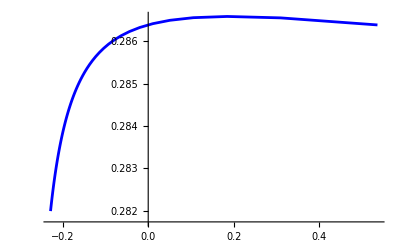

```mathematica
ListPlot[nullVals,Joined->True,PlotStyle->Blue,PlotRange->Full]
```

```mathematica
solDeriv=Quiet@FindRoot[exprEval,{S,initialGuesses[[1]]},
AccuracyGoal->10,
PrecisionGoal->10,
MaxIterations->200000]

NSolve[exprEval==0,S]
```

{S→0.216094}

{{S→0.216094}}

#### Bimolecular

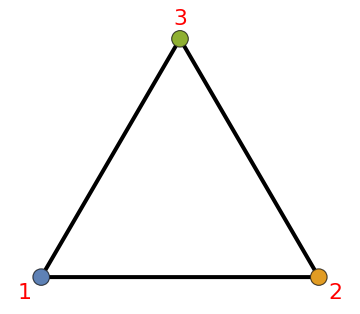

```mathematica
Get["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/CLFunctions.m"];
nNodes = 3;
g = CreateFullGraph[nNodes];
nEdges = Length[EdgeList[g]];

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];

colors = ColorData[97,"ColorList"];
eNums = {3};
e1=Orange;
th = 0.008;
ah =0.07;
(*HighlightGraph[DirectedGraph[g,(*VertexLabels->"Name",*)VertexStyle->Table[i->Directive[colors[[i]],Opacity[1]],{i,1,nNodes}],VertexSize->0.06,EdgeStyle->Directive[Black,Thickness[th],Opacity[1],Arrowheads[ah]],ImageSize->Medium,VertexLabelStyle->Directive[Black,22,Red]],
{Style[edges[[eNums[[1]]]][[2]]->edges[[eNums[[1]]]][[1]],Directive[Thickness[th],e1,Arrowheads[ah]]],
Style[edges[[eNums[[1]]]][[1]]->edges[[eNums[[1]]]][[2]],Directive[Thickness[th],e1,Dashed,Arrowheads[ah]]]
}
]*)
Graph[g,VertexLabels->"Name",VertexStyle->Table[i->Directive[colors[[i]],Opacity[1]],{i,1,nNodes}],VertexSize->0.06,EdgeStyle->Directive[Black,Thickness[th],Opacity[1],Arrowheads[ah]],ImageSize->Medium,VertexLabelStyle->Directive[Black,22,Red]]
```

```mathematica
eq1=W12 pi2 + W13 pi3 - (W21 pi3+W31)pi1==0;
eq2=2*W21 pi1*pi3 + W23 pi3 - (W12+W32)pi2==0;
eq3=W31 pi1+W32 pi2- (W13+W23)pi3-W21 pi3*pi1==0;

eq1=W12 pi2 + W13 pi3 - (W21 pi3+W31)pi1==0;
eq2=W21 pi1*pi3 + W23 pi3 - (W12+W32)pi2==0;
eq3=W31 pi1 +W32 pi2- (W13+W23)pi3==0;

eq4 = pi1+pi2+pi3==1;
Solve[{eq1,eq2,eq3,eq4},{pi1,pi2,pi3}]//Simplify
```

{{pi1→-1/(2 W21 (W31-W32))(W12 W13+W12 W23+W12 W31+W23 W31+W13 W32+W21 W32+W31 W32+√(4 W21 W31 (W12+W32) (W13+W23+W32)+(W23 W31+W12 (W13+W23+W31)+(W13-W21+W31) W32)^2)),pi2→1/(2 W21 (W31-W32) (W13+W23+W32))(W12 W13^2+2 W12 W13 W23+W12 W23^2+2 W12 W13 W31+2 W13 W21 W31+2 W12 W23 W31+W13 W23 W31+2 W21 W23 W31+W23^2 W31+W12 W31^2+W23 W31^2+W13^2 W32-W13 W21 W32+W13 W23 W32-W21 W23 W32+2 W13 W31 W32+W21 W31 W32+W23 W31 W32+W31^2 W32+W13 √(4 W21 W31 (W12+W32) (W13+W23+W32)+(W23 W31+W12 (W13+W23+W31)+(W13-W21+W31) W32)^2)+W23 √(4 W21 W31 (W12+W32) (W13+W23+W32)+(W23 W31+W12 (W13+W23+W31)+(W13-W21+W31) W32)^2)+W31 √(4 W21 W31 (W12+W32) (W13+W23+W32)+(W23 W31+W12 (W13+W23+W31)+(W13-W21+W31) W32)^2)),pi3→-1/(2 W21 (W13+W23+W32))(W12 W13+W12 W23+W12 W31+W23 W31+W13 W32-W21 W32+W31 W32+√(4 W21 W31 (W12+W32) (W13+W23+W32)+(W23 W31+W12 (W13+W23+W31)+(W13-W21+W31) W32)^2))},{pi1→-1/(2 W21 (W31-W32))(W12 W13+W12 W23+W12 W31+W23 W31+W13 W32+W21 W32+W31 W32-√(4 W21 W31 (W12+W32) (W13+W23+W32)+(W23 W31+W12 (W13+W23+W31)+(W13-W21+W31) W32)^2)),pi2→1/(2 W21 (W31-W32) (W13+W23+W32))(W12 W13^2+2 W12 W13 W23+W12 W23^2+2 W12 W13 W31+2 W13 W21 W31+2 W12 W23 W31+W13 W23 W31+2 W21 W23 W31+W23^2 W31+W12 W31^2+W23 W31^2+W13^2 W32-W13 W21 W32+W13 W23 W32-W21 W23 W32+2 W13 W31 W32+W21 W31 W32+W23 W31 W32+W31^2 W32-W13 √(4 W21 W31 (W12+W32) (W13+W23+W32)+(W23 W31+W12 (W13+W23+W31)+(W13-W21+W31) W32)^2)-W23 √(4 W21 W31 (W12+W32) (W13+W23+W32)+(W23 W31+W12 (W13+W23+W31)+(W13-W21+W31) W32)^2)-W31 √(4 W21 W31 (W12+W32) (W13+W23+W32)+(W23 W31+W12 (W13+W23+W31)+(W13-W21+W31) W32)^2)),pi3→-1/(2 W21 (W13+W23+W32))(W12 W13+W12 W23+W12 W31+W23 W31+W13 W32-W21 W32+W31 W32-√(4 W21 W31 (W12+W32) (W13+W23+W32)+(W23 W31+W12 (W13+W23+W31)+(W13-W21+W31) W32)^2))}}

```mathematica
{WijListSym,WjiListSym}=CreateSymblolicListsWij[nNodes,nEdges,edges];

Wijs={1,2,3};
Wjis={4,5,6};
(*Wijs={1,1,1};
Wjis={1,1,1};*)
ff = 2;
Wijs={1,1,0.05Exp[ff/2]};
Wjis={10,0.1,4Exp[-ff/2]};
evalsFunc[sym_,num_]:=Flatten[Table[{sym[[i]]->num[[i]]},{i,1,Length[sym]}],1];
evals = Join[evalsFunc[WijListSym,Wijs],evalsFunc[WjiListSym,Wjis]];

tMax = 20;
eqs={
D[pi1[t],t]==W12 pi2[t] + W13 pi3[t] - (W21 pi3[t]+W31)pi1[t],
D[pi2[t],t]==2*W21 pi1[t]*pi3[t] + W23 pi3[t] - (W12+W32)pi2[t],
D[pi3[t],t]==W31 pi1[t] +W32 pi2[t] - (W13+W23)pi3[t]-W21 pi3[t]*pi1[t],
pi1[0]==1/4,
pi2[0]==0,
pi3[0]==3/4
}/.evals
sol=NDSolve[eqs,{pi1[t],pi2[t],pi3[t]},{t,0,tMax},AccuracyGoal->10,PrecisionGoal->10];

eqs2={
D[pi1[t],t]==W12 pi2[t] + W13 pi3[t] - (W21 pi3[t]+W31)pi1[t],
D[pi2[t],t]==W21 pi1[t]*pi3[t] + W23 pi3[t] - (W12+W32)pi2[t],
D[pi3[t],t]==W31 pi1[t] +W32 pi2[t] - (W13+W23)pi3[t],
pi1[0]==1/2,
pi2[0]==0,
pi3[0]==1/2
}/.evals
sol2=NDSolve[eqs2,{pi1[t],pi2[t],pi3[t]},{t,0,tMax},AccuracyGoal->10,PrecisionGoal->10];
```

{pi1'[t]==pi2[t]+pi3[t]-pi1[t] (0.1+10 pi3[t]),pi2'[t]==-((1+4/ⅇ) pi2[t])+0.135914 pi3[t]+20 pi1[t] pi3[t],pi3'[t]==0.1 pi1[t]+(4 pi2[t])/ⅇ-1.13591 pi3[t]-10 pi1[t] pi3[t],pi1[0]==1/4,pi2[0]==0,pi3[0]==3/4}

{pi1'[t]==pi2[t]+pi3[t]-pi1[t] (0.1+10 pi3[t]),pi2'[t]==-((1+4/ⅇ) pi2[t])+0.135914 pi3[t]+10 pi1[t] pi3[t],pi3'[t]==0.1 pi1[t]+(4 pi2[t])/ⅇ-1.13591 pi3[t],pi1[0]==1/2,pi2[0]==0,pi3[0]==1/2}

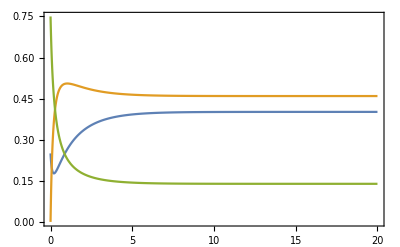

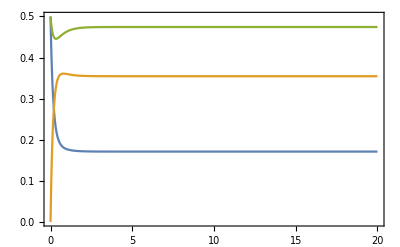

```mathematica
Plot[Evaluate[{pi1[t],pi2[t],pi3[t]}/.sol[[1]]],{t,0,tMax}]
Plot[Evaluate[{pi1[t],pi2[t],pi3[t]}/.sol2[[1]]],{t,0,tMax}]
```

```mathematica
pi1[t]/.sol[[1]]/.{t->tMax}
pi2[t]/.sol[[1]]/.{t->tMax}
pi3[t]/.sol[[1]]/.{t->tMax}
Evaluate[res2]/.{f->ff}

pi1[t]/.sol2[[1]]/.{t->tMax}
pi2[t]/.sol2[[1]]/.{t->tMax}
pi3[t]/.sol2[[1]]/.{t->tMax}
(pi1[t]+pi2[t]+pi3[t])/.sol[[1]]/.{t->tMax}
(pi1[t]+pi2[t]+pi3[t])/.sol[[1]]/.{t->tMax}


Evaluate[res1]/.{f->ff}
```

0.401575

0.459406

0.139019

{0.401576,0.459405,0.139019}

0.171134

0.354528

0.474338

1.

1.

{0.171134,0.354528,0.474338}

#### Bimolecular2

```mathematica
WBA=kBA + kBAR RR;
WAB = kAB + kABR RR;
WCA = kCA+kCAB BB;
WAC = kCA+kABC CC;
WCB = kCB + kCAB AA;
WBC = kBC + kABC CC;

Wmat = {{0, WAB, WAC},{WBA, 0, WBC},{WCA, WCB,0}};
Do[
Wmat[[i,i]]=-Total[Wmat[[;;,i]]]
,{i,1,3}]
pi = Eigenvectors[Wmat][[1]];
pi = pi/Total[pi];
pi[[1]]//Simplify//Numerator
```

kAB (kBC+kCA)+AA kCA kCAB+kCA kCB+kABR kBC RR+kABR kCA RR+CC kABC (2 kAB+AA kCAB+kCB+2 kABR RR)

```mathematica
Wmat//MatrixForm
```

(-kBA-kCA-BB kCAB-kBAR RR | kAB+kABR RR | CC kABC+kCA
kBA+kBAR RR | -kAB-AA kCAB-kCB-kABR RR | CC kABC+kBC
kCA+BB kCAB | AA kCAB+kCB | -2 CC kABC-kBC-kCA)

#### Push-pull

{1<->2,1<->3,1<->4,2<->3,2<->4}

{{2,4}}

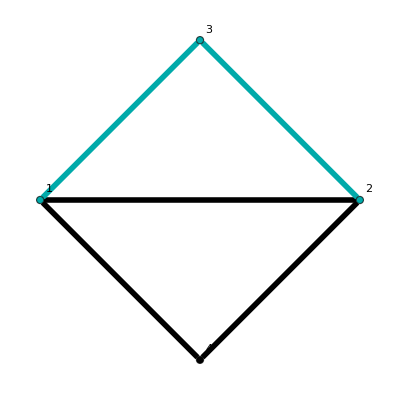

```mathematica
Get["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/CLFunctions.m"];

SeedRandom[36];

adjMat = {{0,0,1,1},{0,0,1,1},{1,1,0,0},{1,1,0,0}};
g = AdjacencyGraph[adjMat];

nn =1;
adjMat = ConstantArray[0,{2+2*nn,2+2*nn}];
Do[
If[Xor[Or[i==1,i==2],Or[j==1,j==2]],adjMat[[i,j]]=1];
,{i,1,2+2*nn},{j,1,2+2*nn}];
adjMat[[1,1]]=0;
adjMat[[2,2]]=0;

adjMat[[1,2]]=1;
adjMat[[2,1]]=1;

g = AdjacencyGraph[adjMat];
edgeList = EdgeList[g];
edgeList

nInput = nn;
nInput =1;
inputInds = {};
Do[
AppendTo[inputInds,1+i];
AppendTo[inputInds,1+(2*nn)+i];
,{i,1,nInput}]

inputInds = {inputInds}
(*edges*)
signs = ConstantArray[1,{2*nInput}];

ex =2;
vCoords={1->{-1,0},2->{1,0}};
Do[
v={0,1-0.15*(i-1)};
AppendTo[vCoords,(2+i)->v];

v={0,-1+0.15*(i-1)};
AppendTo[vCoords,(2+nn+i)->v];
,{i,1,nn}];



(*nn=8;
edgeList = {};
AppendTo[edgeList,1<->3];
Do[
AppendTo[edgeList,(2+i)<->(3+i)];
,{i,1,nn}];
AppendTo[edgeList,(3+nn)<->2];
Do[
AppendTo[edgeList,((3+nn)+i)<->((3+nn+1)+i)];
,{i,1,nn}];
AppendTo[edgeList,1<->(3+nn+1)];
AppendTo[edgeList,(2+2*(nn+1))<->2];

inputInds = {};
Do[
AppendTo[inputInds,i];
,{i,1,nn+2}]
inputInds = {inputInds};
g = Graph[edgeList];
signs=ConstantArray[1,{nn+2}];
signs[[1;;nn/2+1]]=-1;

ex=3;
vCoords={1->{1,0},2->{-1,0}};*)



nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];



pg=HighlightGraph[Graph[g,VertexLabels->"Name",VertexCoordinates->vCoords,VertexStyle->Directive[Black],ImageSize->400,EdgeStyle->Directive[Thickness[0.01],Black,Opacity[1]]],{Style[edgeList[[inputInds[[1]]]],Darker@Cyan],Table[Style[n,Darker@Cyan],{n,1,ex+nn}]}]

ogCoords=GraphEmbedding[Graph[g(*VertexLabels->"Name",*)VertexCoordinates->vCoords]];

(*{dPhidWij,WijMatSymbols}=DPhikDWijMatrix[g,nNodes,nEdges];*)
```

```mathematica
EjList = ConstantArray[0,{nNodes}];
FijList = ConstantArray[0,{nEdges}];
BijList = ConstantArray[0,{nEdges}];

trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArrayRM[trees,edges,inputInds, signs,nEdges,nNodes];
frac=GetpiVecTrees[nNodes,trees,EjList,BijList,FijList,{Log[f]},uiαArray,viαArray][[2]]
```

(6+2 f)/(18+12 f+2 f^2)

```mathematica
((a+b f)/(c+d f+e f^2)/.f->((h+i f)/(j+k f+l f^2)))//Together
```

((j+f k+f^2 l) (b h+b f i+a j+a f k+a f^2 l))/(e h^2+2 e f h i+e f^2 i^2+d h j+d f i j+c j^2+d f h k+d f^2 i k+2 c f j k+c f^2 k^2+d f^2 h l+d f^3 i l+2 c f^2 j l+2 c f^3 k l+c f^4 l^2)

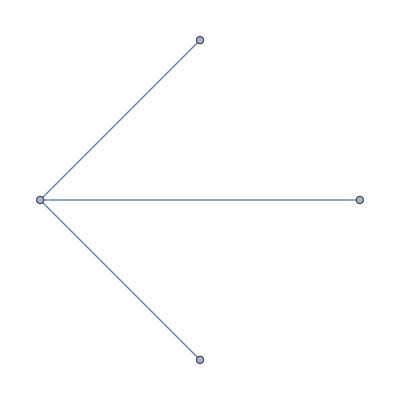
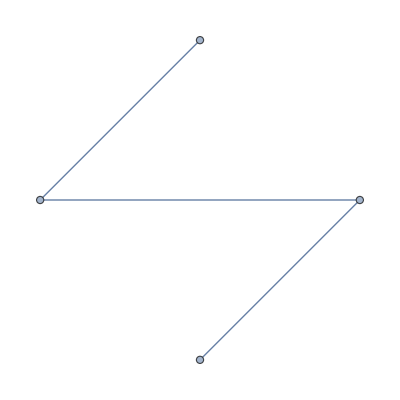
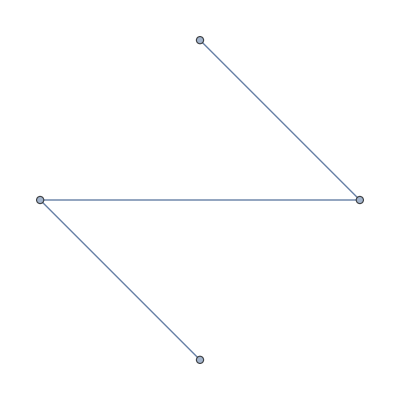
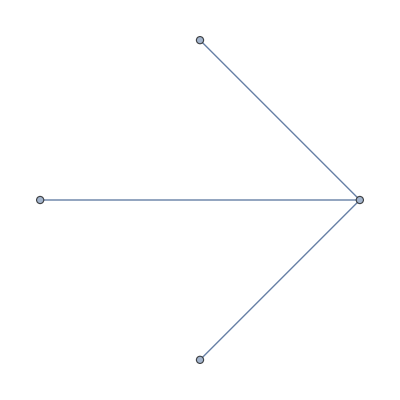
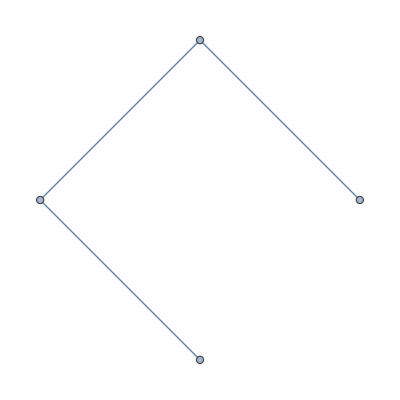
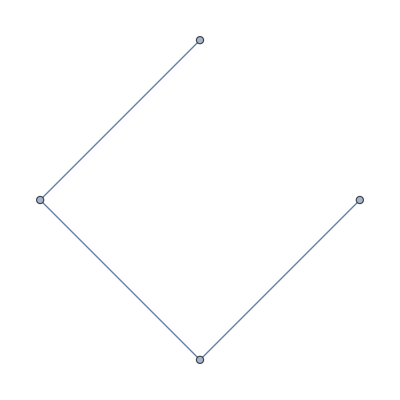
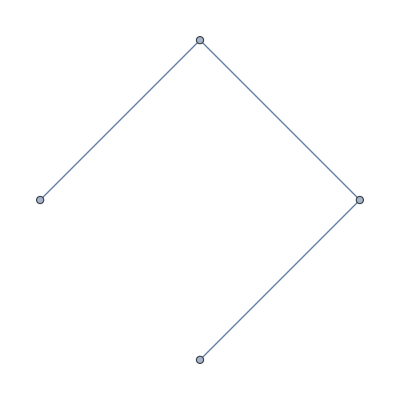
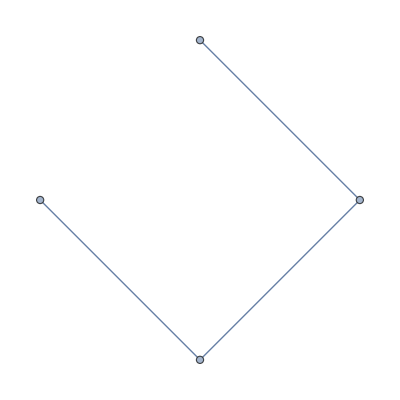

```mathematica
Table[Graph[trees[[m]],VertexCoordinates->vCoords],{m,1,Length[trees]}]
```

```mathematica
(*Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/PushPullParallelTree.png",pg];*)
```

```mathematica
Length[GetSpanningTrees[g,nNodes]]
```

12

```mathematica
trees = GetSpanningTrees[g,nNodes];
```

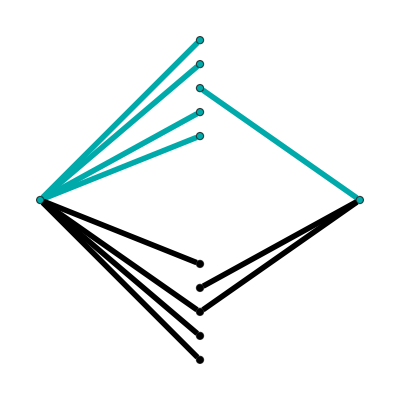

```mathematica
pg=HighlightGraph[Graph[trees[[856]],
VertexCoordinates->vCoords,VertexStyle->Directive[Black],EdgeStyle->Directive[Thickness[0.01],Black,Opacity[1]]],{Style[edgeList[[inputInds[[1]]]],Darker@Cyan],Table[Style[n,Darker@Cyan],{n,1,ex+nn}]}]
```

```mathematica
nNodes = 3;
g = CreateFullGraph[nNodes];
nEdges = Length[EdgeList[g]];

nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];
```

192

```mathematica
Flatten[{{1,2,3},{4,5,6}}]
```

{1,2,3,4,5,6}

```mathematica
Solve[f A^2+(d+e EE - c)A- a + b EE ==0,A]//Simplify
```

{{A→-(-c+d+e EE+√((-c+d+e EE)^2+4 (a-b EE) f))/(2 f)},{A→(c-d-e EE+√((-c+d+e EE)^2+4 (a-b EE) f))/(2 f)}}

```mathematica
D[(-c+d+e EE+√((-c+d+e EE)^2+4 (a-b EE) f))/(2 f),EE]//Simplify
```

(e+(-c e+d e+e^2 EE-2 b f)/(√((-c+d+e EE)^2+4 (a-b EE) f)))/(2 f)

```mathematica
Solve[(e+f EE) A^2+(d EE - b- c EE)A- a EE==0,A]//Simplify
```

{{A→(b+c EE-d EE-√((b+(c-d) EE)^2+4 a EE (e+EE f)))/(2 (e+EE f))},{A→(b+c EE-d EE+√((b+(c-d) EE)^2+4 a EE (e+EE f)))/(2 (e+EE f))}}

```mathematica
Clear[g];
Solve[((a+b EE)+(c+d EE)A)/((e+f EE)+(g+h EE)A) ==A,A]//Simplify
```

{{A→(c-e+d EE-EE f+√((c-e+EE (d-f))^2+4 (a+b EE) (g+EE h)))/(2 (g+EE h))},{A→-(-c+e-d EE+EE f+√((c-e+EE (d-f))^2+4 (a+b EE) (g+EE h)))/(2 (g+EE h))}}

```mathematica
A1=(m0 + m1 x + (m2 x^2+m3 x + m4)^(1/2))/m5;
A2=(m0 + m1 x + (m2 x^2+m3 x + m4)^(1/2))/(m5+m6 x);
D[A1,x]//Simplify
D[A2,x]//FullSimplify
```

(m1+(m3+2 m2 x)/(2 √(m4+x (m3+m2 x))))/m5

((m5+m6 x) (m1+(m3+2 m2 x)/(2 √(m4+x (m3+m2 x))))-m6 (m0+m1 x+√(m4+x (m3+m2 x))))/(m5+m6 x)^2

```mathematica
(*Define the expression*)expr=((m5+m6 x) (m1+(m3+2 m2 x)/(2 Sqrt[m4+x (m3+m2 x)]))-m6 (m0+m1 x+Sqrt[m4+x (m3+m2 x)]))/(m5+m6 x)^2;

(*Simplify assuming all parameters are real*)
FullSimplify[expr,Assumptions->Element[{m0,m1,m2,m3,m4,m5,m6,x},Reals]]//Together
```

(m3 m5-2 m4 m6+2 m2 m5 x-m3 m6 x+2 m1 m5 √(m4+m3 x+m2 x^2)-2 m0 m6 √(m4+m3 x+m2 x^2))/(2 (m5+m6 x)^2 √(m4+m3 x+m2 x^2))

```mathematica
Collect[(d+e EE-c)^2+4(a-b EE),EE]
```

4 a+c^2-2 c d+d^2+(-4 b-2 c e+2 d e) EE+e^2 EE^2

```mathematica
4 a+c^2-2 c d+d^2//Simplify
```

4 a+(c-d)^2

```mathematica
(-4 b-2 c e+2 d e) //Simplify
```

-4 b+2 (-c+d) e

```mathematica
ClearAll["Global`*"];
Solve[S==(a+b S + c R + d S R)/(e + f S + g R + h S R),S]
D[(m0+m1 R + Sqrt[m2 + m3 R + m4 R^2])/(m5 + m6 R),R]//FullSimplify
```

{{S→(b-e+d R-g R-√((-b+e-d R+g R)^2-4 (-a-c R) (f+h R)))/(2 (f+h R))},{S→(b-e+d R-g R+√((-b+e-d R+g R)^2-4 (-a-c R) (f+h R)))/(2 (f+h R))}}

((m5+m6 R) (m1+(m3+2 m4 R)/(2 √(m2+R (m3+m4 R))))-m6 (m0+m1 R+√(m2+R (m3+m4 R))))/(m5+m6 R)^2

```mathematica
(m5+m6 R) (m1+(m3+2 m4 R)/(2 √(m2+R (m3+m4 R))))-m6 (m0+m1 R+√(m2+R (m3+m4 R)))//Simplify
```

```mathematica
((m5+m6 R) (m1+(m3+2 m4 R)/(2 √(m2+R (m3+m4 R))))-m6 (m0+m1 R+√(m2+R (m3+m4 R))))√(m2+R (m3+m4 R))//FullSimplify
```

-m2 m6+m4 m5 R+1/2 m3 (m5-m6 R)+(m1 m5-m0 m6) √(m2+R (m3+m4 R))

```mathematica
Collect[(-(m1 m5-m0 m6) √(m2+R (m3+m4 R)))^2-(-m2 m6+m4 m5 R+1/2 m3 (m5-m6 R))^2//Simplify,R]
```

-1/4 m3^2 m5^2+m2 m3 m5 m6-m2^2 m6^2+m2 (m1 m5-m0 m6)^2+(-m3 m4 m5^2+1/2 m3^2 m5 m6+2 m2 m4 m5 m6-m2 m3 m6^2+m3 (m1 m5-m0 m6)^2) R+(-m4^2 m5^2+m3 m4 m5 m6-(m3^2 m6^2)/4+m4 (m1 m5-m0 m6)^2) R^2

```mathematica
(*Define the m_i variables*)
m0=-(e-b);
m1=-(g-d);
m2=(e-b)^2+4 a f;
m3=2 (e-b) (g-d)+4 (a h+c f);
m4=(g-d)^2+4 c h;
m5=2 f;
m6=2 h;

(*(*Define the n_i variables*)
n0=2 m1 m6-2 m0 m7;
n1=2 m7 m3-m4 m6;
n2=m4 m7-2 m5 m6;

(*Define the polynomial for dS/dR=0*)
poly=(n0^2 m5-n2^2) R^2+(n0^2 m4-2 n1 n2) R+(n0^2 m3-n1^2)//FullSimplify
poly = -1/4 m4^2 m6^2+m3 m4 m6 m7-m3^2 m7^2+m3 (m1 m6-m0 m7)^2+(-m4 m5 m6^2+1/2 m4^2 m6 m7+2 m3 m5 m6 m7-m3 m4 m7^2+m4 (m1 m6-m0 m7)^2) R+(-m5^2 m6^2+m4 m5 m6 m7-(m4^2 m7^2)/4+m5 (m1 m6-m0 m7)^2) R^2//FullSimplify*)

-1/4 m3^2 m5^2+m2 m3 m5 m6-m2^2 m6^2+m2 (m1 m5-m0 m6)^2+(-m3 m4 m5^2+1/2 m3^2 m5 m6+2 m2 m4 m5 m6-m2 m3 m6^2+m3 (m1 m5-m0 m6)^2) R+(-m4^2 m5^2+m3 m4 m5 m6-(m3^2 m6^2)/4+m4 (m1 m5-m0 m6)^2) R^2//FullSimplify
```

16 (a f (d-g)^2-c f (-d e+c f+e g)+b^2 c h+c e^2 h+a b (-d+g) h+a (d e+2 c f-e g) h-a^2 h^2+b c (-d f+f g-2 e h)) (f+h R)^2

```mathematica
Collect[poly,R]
```

64 f^2 (a f (d-g)^2-c f (-d e+c f+e g)+b^2 c h+c e^2 h+a b (-d+g) h+a (d e+2 c f-e g) h-a^2 h^2+b c (-d f+f g-2 e h))+128 f h (a f (d-g)^2-c f (-d e+c f+e g)+b^2 c h+c e^2 h+a b (-d+g) h+a (d e+2 c f-e g) h-a^2 h^2+b c (-d f+f g-2 e h)) R+64 h^2 (a f (d-g)^2-c f (-d e+c f+e g)+b^2 c h+c e^2 h+a b (-d+g) h+a (d e+2 c f-e g) h-a^2 h^2+b c (-d f+f g-2 e h)) R^2